## Accreting System with constant opacity and neglecting gas pressure (inner disk of NS or stellar mass BH)

Solve system neglecting gas pressure and with Q^-=Q^+

```mathematica
Remove["Global`*"]
$Assumptions=R>0 && G>0 && M>0 && Mdot>0 && α>0 &&ρc>0 && Tc>0 && a>0 && μ>0 && Rs>0 &&κR>0 && cs>0 && a >0 &&H>0 && Ωk>0 && R>Rs && c>0 && σ>0&&Ωk>0;
eqns={Σ==ρc H(*,Ωk^2==(G M)/R^3,f4==1-(Rs/R)^(1/2)*),H==cs/Ωk,cs^2==Pc/ρc,Pc==(*(ρc k Tc)/μ+*)(4 σ Tc^4)/(3 c),ν Σ==Mdot/(3 π)f4,Qp==1/2 ν Σ (R (3 G M)/(2 √((G M)/R^3) R^4))^2,Qm==(4σ Tc^4)/(3 Σ κR),Qp==Qm,ν==α cs H};
Print["Solution given, Mdot,M,R,α"]
soln=Solve[Eliminate[eqns,{Qp,Qm,cs,Pc,ν}],{Σ,ρc,Tc,H}][[4]];
f4=1-(Rs/R)^(1/2);
Print[Style[soln//FullSimplify//TableForm,20]]
```

Solution given, Mdot,M,R,α

Σ→-(64 c^2 π R^6 Ωk^3)/(27 G^2 M^2 Mdot (-1+√(Rs/R)) α κR^2)
ρc→(512 c^3 π^2 R^9 Ωk^5)/(81 G^3 M^3 Mdot^2 (-1+√(Rs/R))^2 α κR^3)
Tc→((2/3)^(1/4) √c R Ωk)/(G M R α κR σ Ωk)^(1/4)
H→-(3 G M Mdot (-1+√(Rs/R)) κR)/(8 c π R^3 Ωk^2)

## Accreting Systems with Power-law opacity κ_R neglecting Radiation Pressure (outer disk)

This problem can be done by linearizing it in logarithms. 
This would make the problem simpler to do by hand, however, Mathematica can handle the full brunt of high-order polynomial equations

```mathematica
Remove["Global`*"]
$Assumptions=R>0 && G>0 && M>0 && Mdot>0 && α>0 &&ρc>0 && Tc>0 && a>0 && μ>0 && Rs>0 &&κR>0 && cs>0 && a >0 &&H>0 && Ωk>0 && R>Rs && c>0 && σ>0&&Ωk>0 &&mh>0 &&k>0 && n∈Rationals&&m>0&&Qp==Qm&&κo>0&&Σ>0;
system={{1,-1,1,0,0},{0,-3,1,0,Log[3π α]+Log[Ωk]-Log[Mdot]-Log[f4]},{0,-2,2,1,Log[μ]+2Log[Ωk]-Log[k]},{0,-4,2-m,4-n,Log[27]-Log[32]+3Log[Ωk]+Log[α k]}};
MatrixForm[system]
solution=RowReduce[system]//Simplify;
Print["logh   logΣ    logρ    logT"]
Print[MatrixForm[solution]]
```

(1 | -1 | 1 | 0 | 0
0 | -3 | 1 | 0 | -Log[f4]-Log[Mdot]+Log[3 π α]+Log[Ωk]
0 | -2 | 2 | 1 | -Log[k]+Log[μ]+2 Log[Ωk]
0 | -4 | 2-m | 4-n | Log[27]-Log[32]+Log[k α]+3 Log[Ωk])

logh   logΣ    logρ    logT

(1 | 0 | 0 | 0 | (-2 Log[32]+Log[729]+(2+m) Log[f4]-2 (-4+n) Log[k]+2 Log[Mdot]+m Log[Mdot]+2 Log[k α]-2 Log[3 π α]-m Log[3 π α]-8 Log[μ]+2 n Log[μ]-12 Log[Ωk]-m Log[Ωk]+4 n Log[Ωk])/(14+3 m-4 n)
0 | 1 | 0 | 0 | ((6+m-2 n) Log[f4]+(-4+n) Log[k]+6 Log[Mdot]+m Log[Mdot]-2 n Log[Mdot]-6 Log[3 π α]-m Log[3 π α]+2 n Log[3 π α]+4 Log[μ]-n Log[μ]+Log[32/(27 k α Ωk)]-m Log[Ωk])/(14+3 m-4 n)
0 | 0 | 1 | 0 | (-3 Log[27]+3 Log[32]-2 (-2+n) Log[f4]+3 (-4+n) Log[k]+4 Log[Mdot]-2 n Log[Mdot]-3 Log[k α]-4 Log[3 π α]+2 n Log[3 π α]+12 Log[μ]-3 n Log[μ]+11 Log[Ωk]-4 n Log[Ωk])/(14+3 m-4 n)
0 | 0 | 0 | 1 | (4 Log[27]-4 Log[32]+2 (2+m) Log[f4]+(2-3 m) Log[k]+4 Log[Mdot]+2 m Log[Mdot]+4 Log[k α]-4 Log[3 π α]-2 m Log[3 π α]-2 Log[μ]+3 m Log[μ]+4 Log[Ωk]+4 m Log[Ωk])/(14+3 m-4 n))

## The Equations : Σ, T_c, ρ_c,H,τ,κ_R

Solving the basic equations for any power law opacity, with Qm=Qp

#### Calculate the direct solution to the equations. (Best)

```mathematica
Remove["Global`*"]
$Assumptions=True;
$Assumptions=R>0 && G>0 && M>0 && Mdot>0 && α>0 &&ρc>0 && Tc>0 && a>0 && μ>0 && Rs>0 &&κR>0 && cs>0 && a >0 &&H>0 && Ωk>0 && R>Rs && c>0 && σ>0&&Ωk>0 &&mh>0 &&k>0 && n∈Rationals&&m>0&&Qp==Qm&&κo>0&&Σ>0;

eqns={eqn1=Σ==ρc H,eqn2=H==cs/Ωk,eqn3=cs^2==Pc/ρc,eqn4=Pc==(ρc k Tc)/μ(*+(4 σ Tc^4)/(3 c)*),eqn5=ν Σ==Mdot/(3 π)f4,eqn6=Qp==1/2 ν Σ (R (3 G M)/(2 √((G M)/R^3) R^4))^2,eqn7=Qm==(4σ Tc^4)/(3 Σ κR),eqn8=Qp==Qm,eqn9=ν==α cs H,eqn10=κR==κo ρc^m Tc^n};

eqns=Simplify[PowerExpand[Eliminate[eqns,{cs,Pc,ν,Qm,Qp,κR}]]];
{eqn1=H ρc==Σ,eqn2=f4 Mdot ρc^2==3 π α Σ^3 Ωk,eqn3=k Tc ρc^2==μ Σ^2 Ωk^2,eqn4=32 R^3 Tc^4 ρc^2 σ==27 G M Tc^n α κo ρc^m Σ^4 Ωk};
Tc=Tc/.Solve[Eliminate[{eqn2,eqn3},ρc],Tc][[1]];
ρc=ρc/.Solve[{eqn4},ρc][[1]] //PowerExpand//Simplify;
Print["Σ = ",Σ=Σ/.Solve[Simplify[eqn2]//PowerExpand//Simplify,Σ][[1]]/.R->((G M)/Ωk^2)^(1/3)//PowerExpand //Simplify//Expand//Simplify]
Print["H = ",H=Σ/ρc /.R->((G M)/Ωk^2)^(1/3)//PowerExpand //Simplify//Expand//Simplify]
Print["Tc = ",Tc/.R->((G M)/Ωk^2)^(1/3)//PowerExpand //Simplify//Expand//Simplify]
Print["ρc = ",ρc/.R->((G M)/Ωk^2)^(1/3)//PowerExpand //Simplify//Expand//Simplify]
```

Σ = 3^(-(12+m-2 n)/(10+3 m-2 n)) 1024^(1/(10+3 m-2 n)) (f4 Mdot)^((6+m-2 n)/(10+3 m-2 n)) π^(-(6+m-2 n)/(10+3 m-2 n)) α^(-(8+m-2 n)/(10+3 m-2 n)) (k/μ)^((2 (-4+n))/(10+3 m-2 n)) (κo/σ)^(-2/(10+3 m-2 n)) Ωk^(-(-4+m+2 n)/(10+3 m-2 n))

H = 3^((1-m)/(10+3 m-2 n)) 32^(1/(-10-3 m+2 n)) (f4 Mdot)^((2+m)/(10+3 m-2 n)) π^(-(2+m)/(10+3 m-2 n)) α^(-(1+m)/(10+3 m-2 n)) (k/μ)^((4-n)/(10+3 m-2 n)) (σ/κo)^(1/(-10-3 m+2 n)) Ωk^(-(7+m-2 n)/(10+3 m-2 n))

Tc = 3^((2-2 m)/(10+3 m-2 n)) 1024^(1/(-10-3 m+2 n)) (f4 Mdot)^((2 (2+m))/(10+3 m-2 n)) π^(-(2 (2+m))/(10+3 m-2 n)) α^(-(2 (1+m))/(10+3 m-2 n)) (k/μ)^(-(2+3 m)/(10+3 m-2 n)) (κo/σ)^(2/(10+3 m-2 n)) Ωk^((6+4 m)/(10+3 m-2 n))

ρc = 3^((-13+2 n)/(10+3 m-2 n)) 32^(3/(10+3 m-2 n)) (f4 Mdot)^((4-2 n)/(10+3 m-2 n)) π^((2 (-2+n))/(10+3 m-2 n)) α^((-7+2 n)/(10+3 m-2 n)) (k/μ)^((3 (-4+n))/(10+3 m-2 n)) (σ/κo)^(3/(10+3 m-2 n)) Ωk^((11-4 n)/(10+3 m-2 n))

Take final equations and calculate them for each opacity law

#### Quick view of solutions to avoid recalculating the solution

```mathematica
Remove["Global`*"]
$Assumptions=R>0 && G>0 && M>0 && Mdot>0 && α>0 &&ρc>0 && Tc>0 && a>0 && μ>0 && Rs>0 &&κR>0 && cs>0 && a >0 &&H>0 && Ωk>0 && R>Rs && c>0 && σ>0&&Ωk>0 &&mh>0 &&k>0 && n∈Rationals&&m>0&&Qp==Qm&&κo>0&&Σ>0;
(* (*Final Equations for quick access*)
Σ = (1024^(10 + 3*m - 2*n)^(-1)*(f4*Mdot)^((6 + m - 2*n)/(10 + 3*m - 2*n))*(k/μ)^((2*(-4 + n))/(10 + 3*m - 2*n)))/
  (3^((12 + m - 2*n)/(10 + 3*m - 2*n))*Pi^((6 + m - 2*n)/(10 + 3*m - 2*n))*α^((8 + m - 2*n)/(10 + 3*m - 2*n))*(κo/σ)^(2/(10 + 3*m - 2*n))*
   Ωk^((-4 + m + 2*n)/(10 + 3*m - 2*n))) ;
H = (3^((1 - m)/(10 + 3*m - 2*n))*32^(-10 - 3*m + 2*n)^(-1)*(f4*Mdot)^((2 + m)/(10 + 3*m - 2*n))*(k/μ)^((4 - n)/(10 + 3*m - 2*n))*
   (σ/κo)^(-10 - 3*m + 2*n)^(-1))/(Pi^((2 + m)/(10 + 3*m - 2*n))*α^((1 + m)/(10 + 3*m - 2*n))*Ωk^((7 + m - 2*n)/(10 + 3*m - 2*n))) ;
Tc = (3^((2 - 2*m)/(10 + 3*m - 2*n))*1024^(-10 - 3*m + 2*n)^(-1)*(f4*Mdot)^((2*(2 + m))/(10 + 3*m - 2*n))*(κo/σ)^(2/(10 + 3*m - 2*n))*
   Ωk^((6 + 4*m)/(10 + 3*m - 2*n)))/(Pi^((2*(2 + m))/(10 + 3*m - 2*n))*α^((2*(1 + m))/(10 + 3*m - 2*n))*(k/μ)^((2 + 3*m)/(10 + 3*m - 2*n))) ;
ρc = 3^((-13 + 2*n)/(10 + 3*m - 2*n))*32^(3/(10 + 3*m - 2*n))*(f4*Mdot)^((4 - 2*n)/(10 + 3*m - 2*n))*Pi^((2*(-2 + n))/(10 + 3*m - 2*n))*
  α^((-7 + 2*n)/(10 + 3*m - 2*n))*(k/μ)^((3*(-4 + n))/(10 + 3*m - 2*n))*(σ/κo)^(3/(10 + 3*m - 2*n))*Ωk^((11 - 4*n)/(10 + 3*m - 2*n)) ;
*)
```

#### Calculate the equations either from direct solution or by using the quick view for each segment of the opacity law

```mathematica
Z=2*10^-2;
X=72*10^-2;

Print["Molecules"]
rule={κo->10^-1 Z,R->(R Rs),m->(0),n->0};
mol={Σ,Tc,ρc,H,κo ρc^m Σ^m}/.Ωk->(((G M)/R^3))^(1/2)/.f4->1-((Rs/R))^(1/2)/.rule//PowerExpand//Simplify;

Print["H-"]
rule={κo->10^-13,R->(R Rs),m->(1/3),n->4};
hminus={Σ,Tc,ρc,H,κo ρc^m Σ^m}/.Ωk->(((G M)/R^3))^(1/2)/.f4->1-((Rs/R))^(1/2)/.rule//PowerExpand//Simplify;

Print["Kramers"]
rule={κo->(4*10^25)(1+X)(Z+10^-3),R->(R Rs),m->1,n->(-7/2)};
kramer={Σ,Tc,ρc,H,κo ρc^m Σ^m}/.Ωk->(((G M)/R^3))^(1/2)/.f4->1-((Rs/R))^(1/2)/.rule//PowerExpand//Simplify;

Print["Electron Scattering"]
rule={κo->(2*10^-1)(1+X),R->(R Rs),m->0,n->0};
elecs={Σ,Tc,ρc,H,κo ρc^m Σ^m}/.Ωk->(((G M)/R^3))^(1/2)/.f4->1-((Rs/R))^(1/2)/.rule//PowerExpand//Simplify;
```

Molecules

H-

Kramers

Electron Scattering

## Application

### T Tauri Star

Constants

```mathematica
Msun=2*10^33;
Msunperyear=Msun/(π*10^7);
mh=1.67*10^-27;
G=6.673*10^-8;
c=2.998*10^10;
M=1 Msun;
Rs=10^11;
α=.01;
μ=2 mh;
k=1.38*10^-16;
σ=5.67*10^-5;
R=10^logR;
```

#### With 10^-7 M_Sun/yr

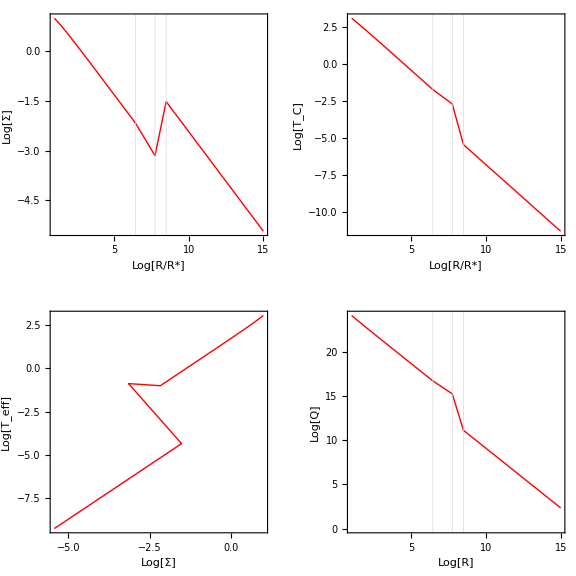

```mathematica
Mdot=10^-7 Msunperyear;

κRm[logR_]=mol[[5]]//Simplify;
κRh[logR_]=hminus[[5]]//Simplify;
κRk[logR_]=kramer[[5]]//Simplify;
κRes[logR_]=elecs[[5]]//Simplify;

(* Find the Place where Subscript[κ, R]'s cross*)

Rh2m=logR/.FindRoot[κRm[logR]==κRh[logR],{logR,8}];
(*LogPlot[{κRm[logR],κRh[logR]},{logR,0,9},GridLines->{{Rh2m},None},PlotLabel->"Opacity",PlotLegends->{"Molecules","H-"}]*)

Rk2h=logR/.FindRoot[κRh[logR]-κRk[logR],{logR,8 }];
(*LogPlot[{κRh[logR],κRk[logR]},{logR,0,9},GridLines->{{Rk2h},None},PlotLabel->"Opacity",PlotLegends->{"H-","Kramers"}]*)

Res2k=logR/.FindRoot[κRk[logR]==κRes[logR],{logR,7 }];
(*LogPlot[{κRk[logR],κRes[logR]},{logR,1,9},GridLines->{{Res2k},None},PlotLabel->"Opacity",PlotLegends->{"Kramers","Electron Scattering"}]*)


(*Enforce continuity*)
kramer=kramer *((elecs/.logR->Res2k)/(kramer/.logR->Res2k));
hminus=hminus*((kramer/.logR->Rk2h)/(hminus/.logR->Rk2h));
mol=mol*((hminus/.logR->Rh2m)/(mol/.logR->Rh2m));
Profiles=Table[Piecewise[{{mol[[i]], logR≥Rh2m}, {hminus[[i]], Rk2h≤logR≤Rh2m}, {kramer[[i]], Res2k≤logR≤Rk2h}, {elecs[[i]], 1≤ logR≤Res2k}}],{i,1,5}];

Clear[Σ,Tc,ρc,H,κR,τ]
Σ[logR_]=Profiles[[1]];
Tc[logR_]=Profiles[[2]];
ρc[logR_]=Profiles[[3]];
H[logR_]=Profiles[[4]];
κR[logR_]=Profiles[[5]];
τ[logR_]=κR[logR]Σ[logR];
Teff[logR_]=(4/(3 Σ[logR] κR[logR]))^(1/4)Tc[logR];
Q[logR_]=(√((k Tc[logR])/μ)*√((G M)/10^(3 logR)))/(π G Σ[logR]);
pt1a=Plot[{Log10[Σ[logR]]},{logR,1,15},GridLines->{{Rh2m,Rk2h,Res2k},None},Exclusions->None,FrameLabel->{"Log[R/R*]","Log[Σ]"},Frame->True,AspectRatio->1,PlotStyle->Red];
pt2a=Plot[{Log10[Tc[logR]]},{logR,1,15},GridLines->{{Rh2m,Rk2h,Res2k},None},Exclusions->None,FrameLabel->{"Log[R/R*]","Log[T_C]"},Frame->True,AspectRatio->1,PlotStyle->Red];
pt3a=ParametricPlot[{Log10[Σ[logR]],Log10[Teff[logR]]},{logR,1,15},Exclusions->None,FrameLabel->{"Log[Σ]","Log[T_eff]"},Frame->True,AspectRatio->1,PlotStyle->Red];
pt4a=Plot[Log10[Q[logR]],{logR,1,15},GridLines->{{Rh2m,Rk2h,Res2k},None},Exclusions->None,FrameLabel->{"Log[R]","Log[Q]"},Frame->True,AspectRatio->1,PlotStyle->Red];
GraphicsGrid[{{pt1a,pt2a},{pt3a,pt4a}},ImageSize->Large]
```

#### With 10^-8 M_Sun/yr

7.68034

6.83992

5.48713

Direct Quantities

Indirect Quantities

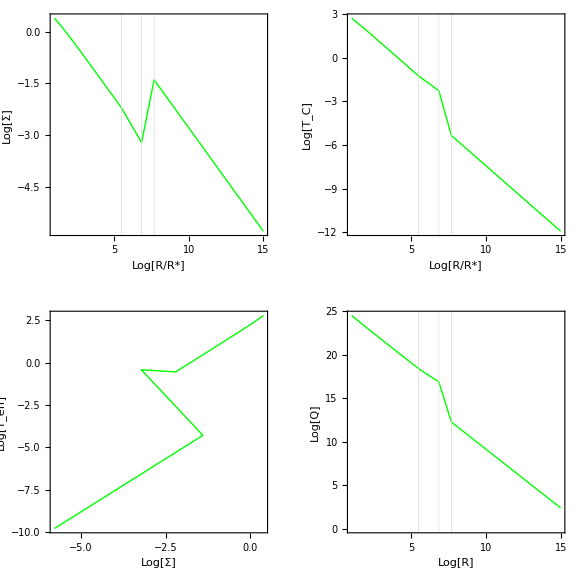

```mathematica
Mdot=10^-8 Msunperyear;

κRm[logR_]=mol[[5]]//Simplify;
κRh[logR_]=hminus[[5]]//Simplify;
κRk[logR_]=kramer[[5]]//Simplify;
κRes[logR_]=elecs[[5]]//Simplify;

Rh2m=logR/.FindRoot[κRm[logR]==κRh[logR],{logR,8}]
(*LogPlot[{κRm[logR],κRh[logR]},{logR,0,9},GridLines->{{Rh2m},None},PlotLabel->"Opacity",PlotLegends->{"Molecules","H-"}]*)

Rk2h=logR/.FindRoot[κRh[logR]-κRk[logR],{logR,8 }]
(*LogPlot[{κRh[logR],κRk[logR]},{logR,0,9},GridLines->{{Rk2h},None},PlotLabel->"Opacity",PlotLegends->{"H-","Kramers"}]*)

Res2k=logR/.FindRoot[κRk[logR]==κRes[logR],{logR,7 }]
(*LogPlot[{κRk[logR],κRes[logR]},{logR,1,9},GridLines->{{Res2k},None},PlotLabel->"Opacity",PlotLegends->{"Kramers","Electron Scattering"}]*)


kramer=kramer *((elecs/.logR->Res2k)/(kramer/.logR->Res2k));
hminus=hminus*((kramer/.logR->Rk2h)/(hminus/.logR->Rk2h));
mol=mol*((hminus/.logR->Rh2m)/(mol/.logR->Rh2m));
Profiles=Table[Piecewise[{{mol[[i]], logR≥Rh2m}, {hminus[[i]], Rk2h≤logR≤Rh2m}, {kramer[[i]], Res2k≤logR≤Rk2h}, {elecs[[i]], 1≤ logR≤Res2k}}],{i,1,5}];

Clear[Σ,Tc,ρc,H,κR,τ]
Print["Direct Quantities"]
Σ[logR_]=Profiles[[1]]//PowerExpand//Simplify;
Tc[logR_]=Profiles[[2]]//PowerExpand//Simplify;
ρc[logR_]=Profiles[[3]]//PowerExpand//Simplify;
H[logR_]=Profiles[[4]]//PowerExpand//Simplify;
Print["Indirect Quantities"]
κR[logR_]=Profiles[[5]](*//PowerExpand//Simplify*);
τ[logR_]=κR[logR]Σ[logR](*//PowerExpand//Simplify*);
Teff[logR_]=(4/(3 Σ[logR] κR[logR]))^(1/4)Tc[logR](*//PowerExpand//Simplify*);
Q[logR_]=(√((k Tc[logR])/μ)*√((G M)/10^(3 logR)))/(π G Σ[logR])(*//PowerExpand//Simplify*);
pt1b=Plot[{Log10[Σ[logR]]},{logR,1,15},GridLines->{{Rh2m,Rk2h,Res2k},None},Exclusions->None,FrameLabel->{"Log[R/R*]","Log[Σ]"},Frame->True,AspectRatio->1,PlotStyle->Green];
pt2b=Plot[{Log10[Tc[logR]]},{logR,1,15},GridLines->{{Rh2m,Rk2h,Res2k},None},Exclusions->None,FrameLabel->{"Log[R/R*]","Log[T_C]"},Frame->True,AspectRatio->1,PlotStyle->Green];
pt3b=ParametricPlot[{Log10[Σ[logR]],Log10[Teff[logR]]},{logR,1,15},Exclusions->None,FrameLabel->{"Log[Σ]","Log[T_eff]"},Frame->True,AspectRatio->1,PlotStyle->Green];
pt4b=Plot[Log10[Q[logR]],{logR,1,15},GridLines->{{Rh2m,Rk2h,Res2k},None},Exclusions->None,FrameLabel->{"Log[R]","Log[Q]"},Frame->True,AspectRatio->1,PlotStyle->Green];
GraphicsGrid[{{pt1b,pt2b},{pt3b,pt4b}},ImageSize->Large]
```

#### With 10^-9 M_Sun/yr

7.68034

6.83992

5.48713

Direct Quantities

Indirect Quantities

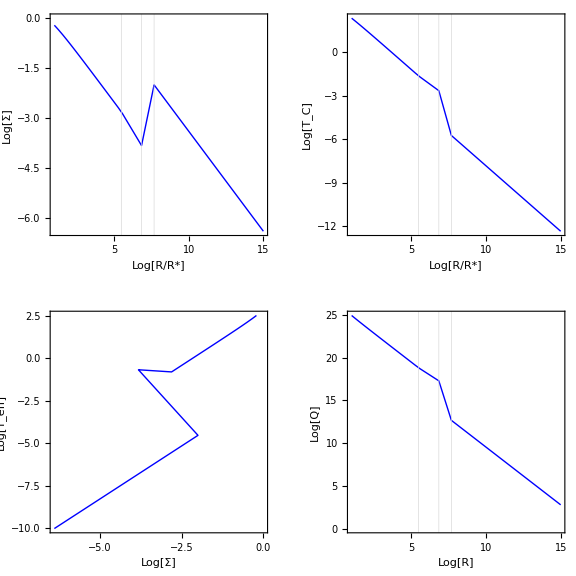

```mathematica
Mdot=10^-9 Msunperyear;

κRm[logR_]=mol[[5]]//Simplify;
κRh[logR_]=hminus[[5]]//Simplify;
κRk[logR_]=kramer[[5]]//Simplify;
κRes[logR_]=elecs[[5]]//Simplify;

Rh2m=logR/.FindRoot[κRm[logR]==κRh[logR],{logR,8}]
(*LogPlot[{κRm[logR],κRh[logR]},{logR,0,9},GridLines->{{Rh2m},None},PlotLabel->"Opacity",PlotLegends->{"Molecules","H-"}]*)

Rk2h=logR/.FindRoot[κRh[logR]-κRk[logR],{logR,8 }]
(*LogPlot[{κRh[logR],κRk[logR]},{logR,0,9},GridLines->{{Rk2h},None},PlotLabel->"Opacity",PlotLegends->{"H-","Kramers"}]*)

Res2k=logR/.FindRoot[κRk[logR]==κRes[logR],{logR,7 }]
(*LogPlot[{κRk[logR],κRes[logR]},{logR,1,9},GridLines->{{Res2k},None},PlotLabel->"Opacity",PlotLegends->{"Kramers","Electron Scattering"}]*)


kramer=kramer *((elecs/.logR->Res2k)/(kramer/.logR->Res2k));
hminus=hminus*((kramer/.logR->Rk2h)/(hminus/.logR->Rk2h));
mol=mol*((hminus/.logR->Rh2m)/(mol/.logR->Rh2m));
Profiles=Table[Piecewise[{{mol[[i]], logR≥Rh2m}, {hminus[[i]], Rk2h≤logR≤Rh2m}, {kramer[[i]], Res2k≤logR≤Rk2h}, {elecs[[i]], 1≤ logR≤Res2k}}],{i,1,5}];

Clear[Σ,Tc,ρc,H,κR,τ]
Print["Direct Quantities"]
Σ[logR_]=Profiles[[1]]//PowerExpand//Simplify;
Tc[logR_]=Profiles[[2]]//PowerExpand//Simplify;
ρc[logR_]=Profiles[[3]]//PowerExpand//Simplify;
H[logR_]=Profiles[[4]]//PowerExpand//Simplify;
Print["Indirect Quantities"]
κR[logR_]=Profiles[[5]](*//PowerExpand//Simplify*);
τ[logR_]=κR[logR]Σ[logR](*//PowerExpand//Simplify*);
Teff[logR_]=(4/(3 Σ[logR] κR[logR]))^(1/4)Tc[logR](*//PowerExpand//Simplify*);
Q[logR_]=(√((k Tc[logR])/μ)*√((G M)/10^(3 logR)))/(π G Σ[logR])(*//PowerExpand//Simplify*);
pt1c=Plot[{Log10[Σ[logR]]},{logR,1,15},GridLines->{{Rh2m,Rk2h,Res2k},None},Exclusions->None,FrameLabel->{"Log[R/R*]","Log[Σ]"},Frame->True,AspectRatio->1,PlotStyle->Blue];
pt2c=Plot[{Log10[Tc[logR]]},{logR,1,15},GridLines->{{Rh2m,Rk2h,Res2k},None},Exclusions->None,FrameLabel->{"Log[R/R*]","Log[T_C]"},Frame->True,AspectRatio->1,PlotStyle->Blue];
pt3c=ParametricPlot[{Log10[Σ[logR]],Log10[Teff[logR]]},{logR,1,15},Exclusions->None,FrameLabel->{"Log[Σ]","Log[T_eff]"},Frame->True,AspectRatio->1,PlotStyle->Blue];
pt4c=Plot[Log10[Q[logR]],{logR,1,15},GridLines->{{Rh2m,Rk2h,Res2k},None},Exclusions->None,FrameLabel->{"Log[R]","Log[Q]"},Frame->True,AspectRatio->1,PlotStyle->Blue];
GraphicsGrid[{{pt1c,pt2c},{pt3c,pt4c}},ImageSize->Large]
```

### Plots

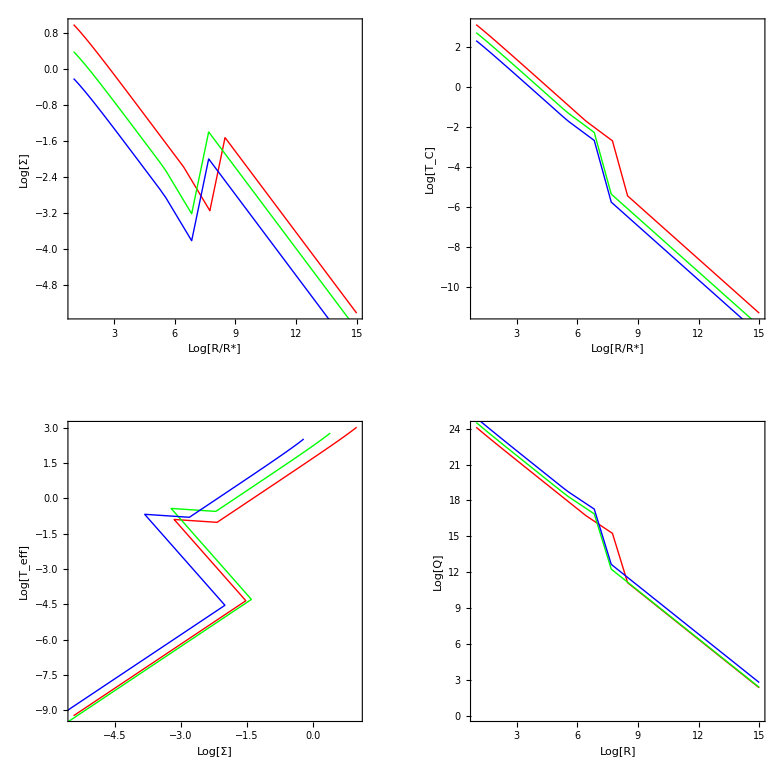

```mathematica
p1=Show[pt1a,pt1b,pt1c,GridLines->None,Axes->None];
p2=Show[pt2a,pt2b,pt2c,GridLines->None,Axes->None];
p3=Show[pt3a,pt3b,pt3c,GridLines->None,Axes->None];
p4=Show[pt4a,pt4b,pt4c,GridLines->None,Axes->None];
GraphicsGrid[{{p1,p2},{p3,p4}},PlotLabel->"Difference Accretion Rates"]
```

## Number 2

```mathematica
Remove["Global`*"]
$Assumptions=True;
$Assumptions=R>0 && G>0 && M>0 && Mdot>0 && α>0 &&ρc>0 && Tc>0 && a>0 && μ>0 && Rs>0 &&κR>0 && cs>0 && a >0 &&H>0 && Ωk>0 && R>Rs && c>0 && σ>0&&Ωk>0 &&mh>0 &&k>0 && n∈Rationals&&m>0&κo>0&&Σ>0;
(*Ωk==((G M)/R^3)^(1/2)
f4=1-√(Rs/R)*)
eqns={eqn1=Σ==ρc +H,eqn2=H==cs-(1/2)(G+M-3R),eqn3=2cs==Pc-ρc,eqn4=Pc==2Log[2]-Log[3]-c+4 Tc+σ,eqn5=ν +Σ==Mdot+Log[3π] +f4,eqn6=Qp==-3Log[2]+2Log[3]+ G+M-3R+ν+Σ,eqn7=Qm==2Log[2]-Log[3]+3Tc-κR+σ+Σ,eqn9=ν==α+ cs+ H(*,eqn10=κR==κo ρc^m Tc^n*)};
```

```mathematica
Eliminate[eqns,{ν,Pc,cs,ρc,Σ,H,f4}]/.Qp-> (ΔQ-Qm) //Simplify
Solve[%,ΔQ]
```

4 c+G+M+2 ΔQ+2 κR==3 R+22 Tc+2 α+6 σ+Log[64/9]

{{ΔQ→1/2 (-4 c-G-M+3 R+22 Tc+2 α-2 κR+6 σ+Log[64/9])}}

```mathematica
.
```

```mathematica
Log[1/2 ν Σ (R (3 G M)/(2 √((G M)/R^3) R^4))^2]//Expand//PowerExpand
```

-3 Log[2]+2 Log[3]+Log[G]+Log[M]-3 Log[R]+Log[ν]+Log[Σ]

```mathematica
Log[1-√(Rs/R)]//Expand//PowerExpand
```

Log[1-(√Rs)/(√R)]